#### 2D shape function

```mathematica
Clear["Global`*"]
(*Gamma function and its values at zero*)
γ[η_,m_,n_]:=Abs[1-(1-((η+1)/2)^2)^m]^n
γ01[m_,n_]:=γ[0,m,n]
γ02[m_,n_]:=γ[0,m,n]
NAG3one[η_,m_,n_]:=(-γ01[m,n]+(γ01[m,n]-1) η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3two[η_,m_,n_]:=(1+η-2 γ[η,m,n])/(1-2 γ01[m,n])
NAG3three[η_,m_,n_]:=(-γ01[m,n]-γ01[m,n] η+γ[η,m,n])/(1-2 γ01[m,n])

(*2D AG-9C shape functions using (m1,n1) for η1 and (m2,n2) for η2*)
NAG9c31[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3one[η1,m1,n1]*NAG3one[η2,m2,n2]
NAG9c32[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3three[η1,m1,n1]*NAG3one[η2,m2,n2]
NAG9c33[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3three[η1,m1,n1]*NAG3three[η2,m2,n2]
NAG9c34[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3one[η1,m1,n1]*NAG3three[η2,m2,n2]
NAG9c35[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3two[η1,m1,n1]*NAG3one[η2,m2,n2]
NAG9c36[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3three[η1,m1,n1]*NAG3two[η2,m2,n2]
NAG9c37[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3two[η1,m1,n1]*NAG3three[η2,m2,n2]
NAG9c38[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3one[η1,m1,n1]*NAG3two[η2,m2,n2]
NAG9c39[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3two[η1,m1,n1]*NAG3two[η2,m2,n2]

(*2D AG-9C shape functions using (m1,n1) for η1 and (m2,n2) for η2*)
NAG9c41[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3three[-η1,m1,n1]*NAG3one[η2,m2,n2]
NAG9c42[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3one[-η1,m1,n1]*NAG3one[η2,m2,n2]
NAG9c43[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3one[-η1,m1,n1]*NAG3three[η2,m2,n2]
NAG9c44[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3three[-η1,m1,n1]*NAG3three[η2,m2,n2]
NAG9c45[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3two[-η1,m1,n1]*NAG3one[η2,m2,n2]
NAG9c46[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3one[-η1,m1,n1]*NAG3two[η2,m2,n2]
NAG9c47[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3two[-η1,m1,n1]*NAG3three[η2,m2,n2]
NAG9c48[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3three[-η1,m1,n1]*NAG3two[η2,m2,n2]
NAG9c49[η1_,η2_,m1_,n1_,m2_,n2_]:=NAG3two[-η1,m1,n1]*NAG3two[η2,m2,n2]

(***)
Nshapec3[η1_,η2_,m1_,n1_,m2_,n2_]:={
NAG9c31[η1,η2,m1,n1,m1,n1],(*N1:node 1 (-1,-1)*)
NAG9c32[η1,η2,m1,n1,m2,n2],(*N2:node 2 (+1,-1)*)
NAG9c33[η1,η2,m1,n1,m2,n2],(*N3:node 3 (+1,+1)*)
NAG9c34[η1,η2,m1,n1,m2,n2],(*N4:node 4 (-1,+1)*)
NAG9c35[η1,η2,m1,n1,m2,n2],(*N5:node 5 (0,-1)*)
NAG9c36[η1,η2,m1,n1,m2,n2],(*N6:node 6 (+1,0)*)
NAG9c37[η1,η2,m1,n1,m2,n2],(*N7:node 7 (0,+1)*)
NAG9c38[η1,η2,m1,n1,m2,n2],(*N8:node 8 (-1,0)*)
NAG9c39[η1,η2,m1,n1,m2,n2] (*N9:node 9 (0,0)*)
};
(***)
Nshapec4[η1_,η2_,m1_,n1_,m2_,n2_]:={
NAG9c41[η1,η2,m1,n1,m2,n2],(*N1:node 1 (-1,-1)*)
NAG9c42[η1,η2,m1,n1,m2,n2],(*N2:node 2 (+1,-1)*)
NAG9c43[η1,η2,m1,n1,m2,n2],(*N3:node 3 (+1,+1)*)
NAG9c44[η1,η2,m1,n1,m2,n2],(*N4:node 4 (-1,+1)*)
NAG9c45[η1,η2,m1,n1,m2,n2],(*N5:node 5 (0,-1)*)
NAG9c46[η1,η2,m1,n1,m2,n2],(*N6:node 6 (+1,0)*)
NAG9c47[η1,η2,m1,n1,m2,n2],(*N7:node 7 (0,+1)*)
NAG9c48[η1,η2,m1,n1,m2,n2],(*N8:node 8 (-1,0)*)
NAG9c49[η1,η2,m1,n1,m2,n2] (*N9:node 9 (0,0)*)
};

(*Shape function for AG type 1*)
NShape[η_,m_,n_]:={NAG3one[η,m,n],NAG3two[η,m,n],NAG3three[η,m,n]};
dNShape[η_,m_,n_]:=D[NShape[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(*Shape function for AG type 2*)
NShape2[η_,m_,n_]:={NAG3t2one[η,m,n],NAG3t2two[η,m,n],NAG3t2three[η,m,n]};
dNShape2[η_,m_,n_]:=D[NShape2[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(***************************************************************)
(*Function to get the M matrices: relate Nodal force and Nodal traction*)
elementMmatrix[xpos_,AGtype_]:= Module[{},
{m,n,type}={AGtype[[1]],AGtype[[2]],AGtype[[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
(*Print[AGshape[η,m,n]];*)
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
M=Table[NIntegrate[AGshape[η,m,n][[j]]*AGshape[η,m,n][[i]]*jac,{η,-1,1}],{i,1,3},{j,1,3}]
];
```

#### Functions to invert from nodal force to traction

```mathematica
Clear["Global`*"]
(*Gamma function and its values at zero*)
γ[η_,m_,n_]:=Abs[1-(1-((η+1)/2)^2)^m]^n
γ01[m_,n_]:=γ[0,m,n]
γ02[m_,n_]:=γ[0,m,n]
NAG3one[η_,m_,n_]:=(-γ01[m,n]+(γ01[m,n]-1) η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3two[η_,m_,n_]:=(1+η-2 γ[η,m,n])/(1-2 γ01[m,n])
NAG3three[η_,m_,n_]:=(-γ01[m,n]-γ01[m,n] η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3t2one[η_,m_,n_]:=NAG3three[-η,m,n]
NAG3t2two[η_,m_,n_]:=NAG3two[-η,m,n]
NAG3t2three[η_,m_,n_]:=NAG3one[-η,m,n]
(*Shape function for AG type 1*)
NShape[η_,m_,n_]:={NAG3one[η,m,n],NAG3two[η,m,n],NAG3three[η,m,n]};
dNShape[η_,m_,n_]:=D[NShape[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(*Shape function for AG type 2*)
NShape2[η_,m_,n_]:={NAG3t2one[η,m,n],NAG3t2two[η,m,n],NAG3t2three[η,m,n]};
dNShape2[η_,m_,n_]:=D[NShape2[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(***************************************************************)
(*Function to get the M matrices: relate Nodal force and Nodal traction*)
elementMmatrix[xpos_,AGtype_]:= Module[{},
{m,n,type}={AGtype[[1]],AGtype[[2]],AGtype[[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
(*Print[AGshape[η,m,n]];*)
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
M=Table[NIntegrate[AGshape[η,m,n][[j]]*AGshape[η,m,n][[i]]*jac,{η,-1,1}],{i,1,3},{j,1,3}]
];
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
GlobalMmat[xcoord_,conns_,AGtype_]:=Module[{n=Max@Flatten@conns,GlobalMat,Me,conn},
GlobalMat=ConstantArray[0.,{n,n}];
Do[
Me=elementMmatrix[xcoord[[e]],AGtype[[e]]];
(*Print[Me//MatrixForm];*)
conn=conns[[e]];
Do[
GlobalMat[[conn[[i]],conn[[j]]]]+=Me[[i,j]],{i,3},{j,3}],
{e,Length@conns}];
GlobalMat  (* <--return M assembled*)
]
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
PxinterpolatedData[Pvec_,AGtype_,xcoord_]:=Module[{},
Pxdata={};
(*total=0;*)
Pelem=Partition[Pvec,3,2];
nelem= Length[conns];
Do[
elem=e;
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};
If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
Clear[x,η];
xη=AGshape[η,1,1].xcoord[[elem]];
ηmap=η/.NSolve[xη==x,η]//First;
PinterpolatePhysical=Sum[AGshape[η,m,n][[i]]*Pelem[[elem]][[i]],{i,1,3}]/.{η->ηmap};(*geometric mapping*)
(*resultant=NIntegrate[PinterpolatePhysical,{x,xmin,xmax}];
PxResultant=total+resultant;*)

{xmin,xmax}={Min[xcoord[[elem]]],Max[xcoord[[elem]]]};
n=100;
dx=(xmax-xmin)/n;
xdata=Table[xmin+i dx,{i,0,n}];
pdata=PinterpolatePhysical/.x->xdata;
plotdata=Transpose[{xdata, pdata}];
Pxdata=AppendTo[Pxdata, plotdata];
,{e,1,nelem}];
Print[PxResultant];
Flatten[Pxdata,1]
]


ComputeResultant[Pelem_,xcoord_,AGtype_]:=Module[{},
totalResutant=0;
Do[
elem=e;
xpos=xcoord[[elem]];
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];

resultant=Pelem[[elem]].NIntegrate[AGshape[η,m,n]*jac,{η,-1,1}];
(*Print[resultant];*)
totalResutant=totalResutant+resultant;
,{e,1,Length[conns]}];
totalResutant
]
```

#### Build element nodal force map

```mathematica
Clear["Global`*"]
```

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
elenodalforce="ElementForce.xlsx";
conn="connectivity_Q9_40x40.xlsx";
coord="nodal_displacement_disp_control_(1,10).xlsx";

forcedata=Import[FileNameJoin[{dir2,elenodalforce}]];
conndata=Import[FileNameJoin[{dir2,conn}]];
coorddata=Import[FileNameJoin[{dir2,coord}]];

forceRest=Rest[forcedata[[1]]];
connRest=Rest[conndata[[1]]];
coordRest=Rest[coorddata[[1]]];

forceele={};
forceelewithid={};

Do[
eleid=j;

eleforce=forceRest[[eleid+1]];
eleconn=connRest[[eleid+1]];

forceeledata=Table[{eleconn[[n+1]],eleforce[[2n]],eleforce[[2n+1]]},{n,1,9}];
AppendTo[forceelewithid,{eleid,forceeledata}];
,{j,0,1599}]

forceelewithid//MatrixForm;

elemid=760;
forceelewithid[[elemid+1]]
```

{760,{{3078.,84.3165,118359.},{3080.,12285.3,117772.},{3242.,-12292.5,-130602.},{3240.,-102.061,-105547.},{3079.,23860.1,495244.},{3161.,1915.27,-48731.7},{3241.,-25750.5,-446495.},{3159.,3.72529×10^-9,1.11759×10^-8},{3160.,7.45058×10^-9,-2.6077×10^-8}}}

```mathematica
(*Extract element in row and column*)
nx=40;ny=40;

getElemRow[connectivity_,nx_,ey_]:=Module[{s,e},s=ey*nx+1;
e=(ey+1)*nx;
connectivity[[s;;e]]];

getElemCol[connectivity_,nx_,ny_,ex_]:=connectivity[[ex+1;;nx*ny;;nx]];

row=0;
col=0;

rowconn=getElemRow[connRest,nx,row];
colconn=getElemCol[connRest,nx,ny,col];

rowlist=rowconn[[All,1]];
collist=colconn[[All,1]];

datarow=forceelewithid[[rowlist+1]][[All,2]];
datacol=forceelewithid[[collist+1]][[All,2]];

fxvert=datacol[[All,{1,8,4},2]] ;
fyvert=datacol[[All,{4,7,3},3]];(*Based on columns*)
fxhorz=datarow[[All,{1,8,4},2]] ;
fyhorz=datarow[[All,{4,7,3},3]];(*Based on rows*)

Ne=Length[fxhorz];
Fgxvert=ConstantArray[0,2 Ne+1];
Fgyvert=ConstantArray[0,2 Ne+1];
Fgxhorz=ConstantArray[0,2 Ne+1];
Fgyhorz=ConstantArray[0,2 Ne+1];
Do[
Fgxhorz[[{2 e-1,2 e,2 e+1}]]+=fxhorz[[e]];
Fgyhorz[[{2 e-1,2 e,2 e+1}]]+=fyhorz[[e]];
Fgxvert[[{2 e-1,2 e,2 e+1}]]+=fxvert[[e]];
Fgyvert[[{2 e-1,2 e,2 e+1}]]+=fyvert[[e]];
,{e,1,40}];

(*ListLinePlot[{Fgxhorz,Fgyhorz}]
ListLinePlot[{Fgxvert,Fgyvert}]*)

(*Extract nodal coord*)
nodevert=datacol[[All,{1,8,4},1]];(*Based on row*)
nodehorz=datarow[[All,{4,7,3},1]];(*Based on row*)

nodevertAssembled=DeleteDuplicates@Flatten[nodevert];
nodehorzAssembled=DeleteDuplicates@Flatten[nodehorz];

coordvert=coordRest[[nodevertAssembled+1,{1,2,3}]];
coordhorz=coordRest[[nodehorzAssembled+1,{1,2,3}]];

datavert=MapThread[Append,{MapThread[Append,{coordvert,Fgxvert}],Fgyvert}];
datahorz=MapThread[Append,{MapThread[Append,{coordhorz,Fgxhorz}],Fgyhorz}];

datavertwHeader=Prepend[datavert,{"nodeID(vert,col="<>ToString[col]<>")","x","y","Fgx","Fgy"}]//MatrixForm;
datahorzwHeader=Prepend[datahorz,{"nodeID(horz,row="<>ToString[row]<>")","x","y","Fgx","Fgy"}]//MatrixForm
```

(nodeID(horz,row=0) | x | y | Fgx | Fgy
162. | 0. | 0.25 | 383690. | -391425.
163. | 0.125 | 0.25 | 4.65661×10^-10 | -1.54423×10^6
164. | 0.25 | 0.25 | 232890. | -736474.
165. | 0.375 | 0.25 | 394712. | -1.30931×10^6
166. | 0.5 | 0.25 | 178280. | -607052.
167. | 0.625 | 0.25 | 421208. | -1.15242×10^6
168. | 0.75 | 0.25 | 187222. | -550953.
169. | 0.875 | 0.25 | 412270. | -1.06907×10^6
170. | 1. | 0.25 | 189557. | -520357.
171. | 1.125 | 0.25 | 402469. | -1.02175×10^6
172. | 1.25 | 0.25 | 189547. | -502570.
173. | 1.375 | 0.25 | 395411. | -994075.
174. | 1.5 | 0.25 | 189129. | -492207.
175. | 1.625 | 0.25 | 390891. | -978303.
176. | 1.75 | 0.25 | 188867. | -486549.
177. | 1.875 | 0.25 | 388325. | -970284.
178. | 2. | 0.25 | 188885. | -484040.
179. | 2.125 | 0.25 | 387212. | -967525.
180. | 2.25 | 0.25 | 189169. | -483694.
181. | 2.375 | 0.25 | 387162. | -968386.
182. | 2.5 | 0.25 | 189665. | -484834.
183. | 2.625 | 0.25 | 387871. | -971705.
184. | 2.75 | 0.25 | 190311. | -486962.
185. | 2.875 | 0.25 | 389098. | -976607.
186. | 3. | 0.25 | 191047. | -489696.
187. | 3.125 | 0.25 | 390649. | -982407.
188. | 3.25 | 0.25 | 191817. | -492731.
189. | 3.375 | 0.25 | 392360. | -988556.
190. | 3.5 | 0.25 | 192573. | -495819.
191. | 3.625 | 0.25 | 394098. | -994602.
192. | 3.75 | 0.25 | 193274. | -498756.
193. | 3.875 | 0.25 | 395751. | -1.00018×10^6
194. | 4. | 0.25 | 193884. | -501377.
195. | 4.125 | 0.25 | 397226. | -1.00499×10^6
196. | 4.25 | 0.25 | 194375. | -503551.
197. | 4.375 | 0.25 | 398449. | -1.00879×10^6
198. | 4.5 | 0.25 | 194726. | -505174.
199. | 4.625 | 0.25 | 399363. | -1.01142×10^6
200. | 4.75 | 0.25 | 194923. | -506177.
201. | 4.875 | 0.25 | 399928. | -1.01277×10^6
202. | 5. | 0.25 | 194957. | -506516.
203. | 5.125 | 0.25 | 400119. | -1.01277×10^6
204. | 5.25 | 0.25 | 194827. | -506177.
205. | 5.375 | 0.25 | 399928. | -1.01142×10^6
206. | 5.5 | 0.25 | 194539. | -505174.
207. | 5.625 | 0.25 | 399363. | -1.00879×10^6
208. | 5.75 | 0.25 | 194105. | -503551.
209. | 5.875 | 0.25 | 398449. | -1.00499×10^6
210. | 6. | 0.25 | 193544. | -501377.
211. | 6.125 | 0.25 | 397226. | -1.00018×10^6
212. | 6.25 | 0.25 | 192883. | -498756.
213. | 6.375 | 0.25 | 395751. | -994602.
214. | 6.5 | 0.25 | 192156. | -495819.
215. | 6.625 | 0.25 | 394098. | -988556.
216. | 6.75 | 0.25 | 191403. | -492731.
217. | 6.875 | 0.25 | 392360. | -982407.
218. | 7. | 0.25 | 190674. | -489696.
219. | 7.125 | 0.25 | 390649. | -976607.
220. | 7.25 | 0.25 | 190029. | -486962.
221. | 7.375 | 0.25 | 389098. | -971705.
222. | 7.5 | 0.25 | 189540. | -484834.
223. | 7.625 | 0.25 | 387871. | -968386.
224. | 7.75 | 0.25 | 189292. | -483694.
225. | 7.875 | 0.25 | 387162. | -967525.
226. | 8. | 0.25 | 189392. | -484040.
227. | 8.125 | 0.25 | 387212. | -970284.
228. | 8.25 | 0.25 | 189976. | -486549.
229. | 8.375 | 0.25 | 388325. | -978303.
230. | 8.5 | 0.25 | 191223. | -492207.
231. | 8.625 | 0.25 | 390891. | -994075.
232. | 8.75 | 0.25 | 193379. | -502570.
233. | 8.875 | 0.25 | 395411. | -1.02175×10^6
234. | 9. | 0.25 | 196784. | -520357.
235. | 9.125 | 0.25 | 402469. | -1.06907×10^6
236. | 9.25 | 0.25 | 201837. | -550953.
237. | 9.375 | 0.25 | 412270. | -1.15242×10^6
238. | 9.5 | 0.25 | 208077. | -607052.
239. | 9.625 | 0.25 | 421208. | -1.30931×10^6
240. | 9.75 | 0.25 | 202445. | -736474.
241. | 9.875 | 0.25 | 394712. | -1.54423×10^6
242. | 10. | 0.25 | 167940. | -391425.)

#### Test

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
elenodalforce="ElementForce.xlsx";
elenodalforcedata=Import[FileNameJoin[{dir2,elenodalforce}]];

eleforcedata=Drop[Drop[elenodalforcedata[[1]],{1,1}],{1,1}];
fxY95=Take[eleforcedata[[All,{8,14,6}]],{761,800}]; (*top edges of second row from the top*)
fyY95=Take[eleforcedata[[All,{9,15,7}]],{761,800}]; (*top edge of second row from the top*)

eleforcedata[[761]]
fxY95;
```

{760.,84.1265,118681.,12273.6,118091.,-12280.7,-130909.,-101.855,-105881.,23836.3,496505.,1915.1,-48685.7,-25726.6,-447802.,7.45058×10^-9,3.72529×10^-9,1.49012×10^-8,1.11759×10^-8}

{-105881.,-447802.,-236550.,-500585.,-264433.,-558803.,-294683.,-621197.,-326764.,-686830.,-360269.,-754982.,-394879.,-825056.,-430310.,-896495.,-466280.,-968706.,-502474.,-1.041×10^6,-538517.,-1.11255×10^6,-573955.,-1.18238×10^6,-608259.,-1.24934×10^6,-640820.,-1.31216×10^6,-670977.,-1.36948×10^6,-698037.,-1.41993×10^6,-721316.,-1.46216×10^6,-740180.,-1.49501×10^6,-754081.,-1.51748×10^6,-762599.,-1.52889×10^6,-765469.,-1.52889×10^6,-762599.,-1.51748×10^6,-754081.,-1.49501×10^6,-740180.,-1.46216×10^6,-721316.,-1.41993×10^6,-698037.,-1.36948×10^6,-670977.,-1.31216×10^6,-640820.,-1.24934×10^6,-608259.,-1.18238×10^6,-573955.,-1.11255×10^6,-538517.,-1.041×10^6,-502474.,-968706.,-466280.,-896495.,-430310.,-825056.,-394879.,-754982.,-360269.,-686830.,-326764.,-621197.,-294683.,-558803.,-264433.,-500585.,-236550.,-447802.,-105881.}

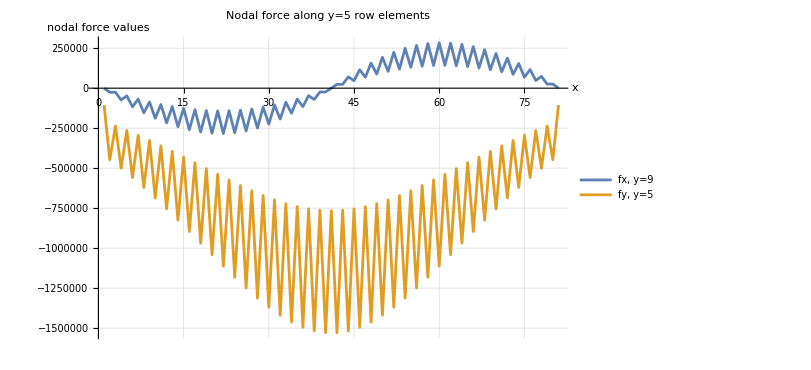

```mathematica
Ne=Length[fxY95];
FgxY95=ConstantArray[0,2 Ne+1];
FgyY95=ConstantArray[0,2 Ne+1];

Do[
FgxY95[[{2 e-1,2 e,2 e+1}]]+=fxY95[[e]];
FgyY95[[{2 e-1,2 e,2 e+1}]]+=fyY95[[e]];
,{e,1,40}];
FgyY95

ListLinePlot[{FgxY95,FgyY95},PlotRange->All,
PlotLegends->Placed[{
Style["fx, y=9",16],Style["fy,  y=5",16],
Style["fx, y=9.5",16],Style["fy,  y=5",16]
},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along y=5 row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[1;;81]];
xcoordglobal=underpunchdata[[All,2]];
Fy=FgyY95;


Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 1};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)
```

{{0.,0.125,0.25},{0.25,0.375,0.5},{0.5,0.625,0.75},{0.75,0.875,1.},{1.,1.125,1.25},{1.25,1.375,1.5},{1.5,1.625,1.75},{1.75,1.875,2.},{2.,2.125,2.25},{2.25,2.375,2.5},{2.5,2.625,2.75},{2.75,2.875,3.},{3.,3.125,3.25},{3.25,3.375,3.5},{3.5,3.625,3.75},{3.75,3.875,4.},{4.,4.125,4.25},{4.25,4.375,4.5},{4.5,4.625,4.75},{4.75,4.875,5.},{5.,5.125,5.25},{5.25,5.375,5.5},{5.5,5.625,5.75},{5.75,5.875,6.},{6.,6.125,6.25},{6.25,6.375,6.5},{6.5,6.625,6.75},{6.75,6.875,7.},{7.,7.125,7.25},{7.25,7.375,7.5},{7.5,7.625,7.75},{7.75,7.875,8.},{8.,8.125,8.25},{8.25,8.375,8.5},{8.5,8.625,8.75},{8.75,8.875,9.},{9.,9.125,9.25},{9.25,9.375,9.5},{9.5,9.625,9.75},{9.75,9.875,10.}}

PxResultant

Nodal traction vectors P(1,1) = {-2.544×10^6,-2.685×10^6,-2.841×10^6,-3.002×10^6,-3.175×10^6,-3.352×10^6,-3.538×10^6,-3.726×10^6,-3.923×10^6,-4.120×10^6,-4.324×10^6,-4.529×10^6,-4.739×10^6,-4.950×10^6,-5.164×10^6,-5.379×10^6,-5.596×10^6,-5.812×10^6,-6.030×10^6,-6.246×10^6,-6.462×10^6,-6.676×10^6,-6.887×10^6,-7.095×10^6,-7.298×10^6,-7.497×10^6,-7.688×10^6,-7.874×10^6,-8.049×10^6,-8.218×10^6,-8.373×10^6,-8.521×10^6,-8.652×10^6,-8.775×10^6,-8.878×10^6,-8.972×10^6,-9.044×10^6,-9.107×10^6,-9.146×10^6,-9.176×10^6,-9.181×10^6,-9.176×10^6,-9.146×10^6,-9.107×10^6,-9.044×10^6,-8.972×10^6,-8.878×10^6,-8.775×10^6,-8.652×10^6,-8.521×10^6,-8.373×10^6,-8.218×10^6,-8.049×10^6,-7.874×10^6,-7.688×10^6,-7.497×10^6,-7.298×10^6,-7.095×10^6,-6.887×10^6,-6.676×10^6,-6.462×10^6,-6.246×10^6,-6.030×10^6,-5.812×10^6,-5.596×10^6,-5.379×10^6,-5.164×10^6,-4.950×10^6,-4.739×10^6,-4.529×10^6,-4.324×10^6,-4.120×10^6,-3.923×10^6,-3.726×10^6,-3.538×10^6,-3.352×10^6,-3.175×10^6,-3.002×10^6,-2.841×10^6,-2.685×10^6,-2.544×10^6}

p(x) resultant force P(1,1) = -6.28497×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2026_01_21_analysis element nodal force, traction\2026_01_21_punch_results\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)\NodalTraction.xlsx

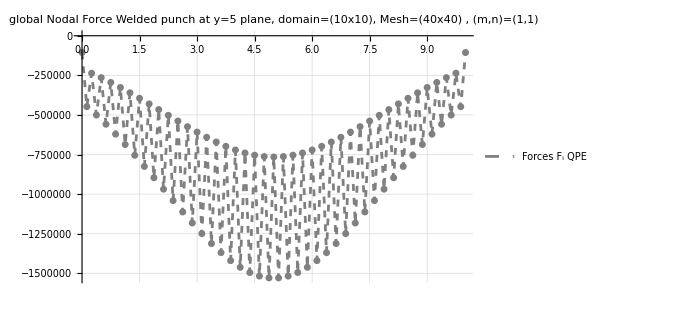

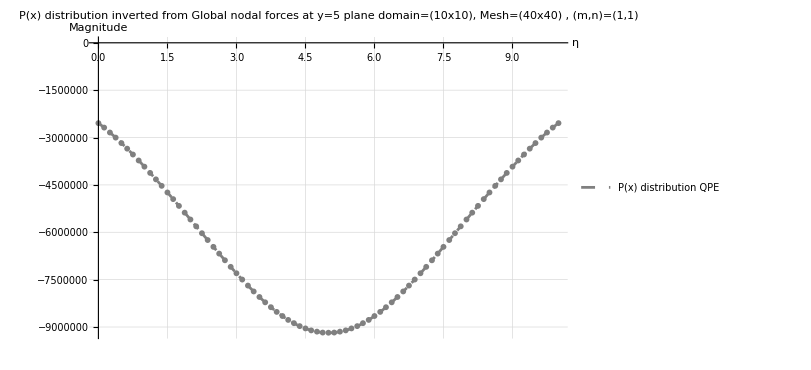

```mathematica
Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```